# Woods-Saxon Potential

## Micah Buuck

6/14/13

## Constants and Initial Conditions

Originally I tried to make use of Mathematica's built-in unit handling, but I couldn't figure out how to make that work with plotting, so I gave up. I left the code for it in, but commented it out.

```mathematica
(*<<Units`
Needs["PhysicalConstants`"]*)
```

```mathematica
R=3 (*Femto Meter*);
V0=-50 (*Mega ElectronVolt*);
a=.54 (*Femto Meter*);
V[r_]:=V0/(1+E^((r-R)/a));
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
```

### Plot for potential

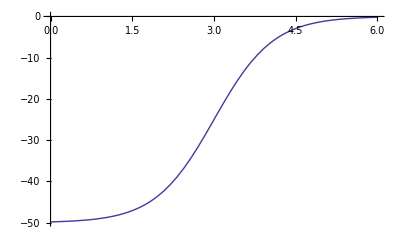

```mathematica
Plot[V[r],{r,0,2*R}]
```

## Solve the Schrödinger Equation

First I solve the Schrödinger equation for the radial wavefunction with an arbitrary constant for the initial condition for u'(0). My goal is to show that the resulting phase shift we get from this in independent of the choice of u'(0).

```mathematica
s[L_,k_,b_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==b},u,{r,(1000*k)^(-1),5*R}]
```

```mathematica
u[L_,k_,r_,b_]:=u[r]/.s[L,k,b][[1]]
```

```mathematica
β[L_,k_,b_]:=5*R/Evaluate[u[L,k,5*R,b]]*(D[u[L,k,r,b],r]/.r->(5*R))-1
tanδ[L_,k_,b_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k,b]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k,b]*SphericalBesselY[L,k*5*R])]
```

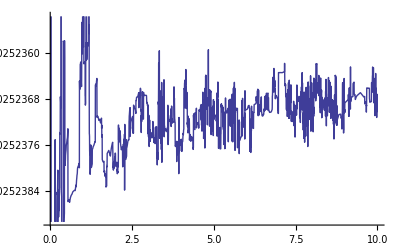

```mathematica
Plot[tanδ[0,1,b],{b,0.01,10}]
```

As we can see from this plot of tanδ vs. u'(0), the phase shift appears to be independent of our choice of u'(0) up to about 0.01% error.

## Reformulate tanδ for specific choice of u'(0)

These are the same equations as above, but now we have chosen u'(0)=8 (an arbitrary choice).

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
β[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k]*SphericalBesselY[L,k*5*R])]
```

```mathematica
Table[tanδ[L,1],{L,0,20}]
```

{-0.498341,-0.740053,-1.40718,-9.04647,0.345919,0.0544545,0.0105089,0.00210731,0.000424391,0.0000852015,0.0000170165,3.39049×10^-6,6.73638×10^-7,1.33352×10^-7,3.30182×10^-8,7.27915×10^-9,1.19763×10^-9,1.49402×10^-10,3.04508×10^-12,-2.23543×10^-12,-3.39837×10^-13}

For k=1, tanδ becomes negligible after about L=5. This is also evident in the plot for continuous L below.

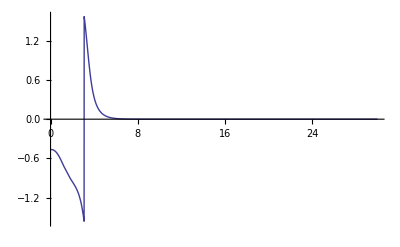

```mathematica
Plot[ArcTan[tanδ[L,1]],{L,0,30},PlotRange->{-Pi/2,Pi/2}]
```

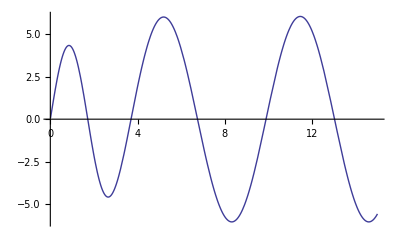

```mathematica
Plot[Evaluate[u[0,1,r]],{r,(100)^(-1),5*R}]
```

Plugging this phase shift into the equations for the scattering amplitude is:

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,2*k*R}]
```

Here is a table of some values of dσ/dΩ as a function of θ.

```mathematica
Clear[dσdΩ]
```

```mathematica
dσdΩ[k_]:=Table[{θ,Abs[f[k,θ]]^2},{θ,0,Pi,.1}]
```

```mathematica
dσdΩ[1]
```

{{0.,158.189},{0.1,150.907},{0.2,130.909},{0.3,103.039},{0.4,73.3582},{0.5,47.173},{0.6,27.6835},{0.7,15.6698},{0.8,10.0428},{0.9,8.76624},{1.,9.67827},{1.1,10.9965},{1.2,11.5373},{1.3,10.7725},{1.4,8.79439},{1.5,6.18042},{1.6,3.73925},{1.7,2.18106},{1.8,1.82782},{1.9,2.48827},{2.,3.55758},{2.1,4.29942},{2.2,4.18732},{2.3,3.15877},{2.4,1.67359},{2.5,0.546581},{2.6,0.612451},{2.7,2.35085},{2.8,5.62532},{2.9,9.6576},{3.,13.2702},{3.1,15.3154}}

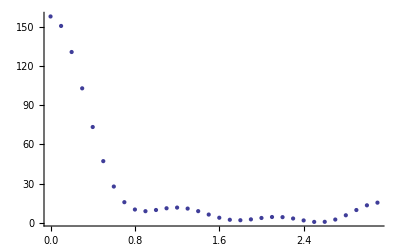

```mathematica
p1=ListPlot[%]
```

Here's a plot of that same information. This takes quite a while to evaluate.

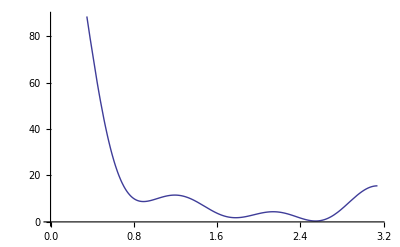

```mathematica
Plot[Abs[f[1,θ]]^2,{θ,0,Pi},PlotRange->{0,160}]
```

## Eikonal Approximation

These equations come straight out of Sakurai, equations 7.4.13 and 7.4.14 (page 394).

```mathematica
Δ[k_,b_?NumericQ]:=-m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,Infinity}]
Eif[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,k*b*θ]*(E^(2*I*Δ[k,b])-1),{b,0,Infinity}]
```

I had to have the iteration of the table below happen in integer steps because doing it in decimal steps was giving Mathematica problems somehow. I think it probably has something to do with differences in the way it handles integers and floats.

```mathematica
eikdσdΩ[k_]:=Table[{θ/10.,Abs[Eif[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eikdσdΩ[1]
```

{{0,161.128},{0.1,150.792},{0.2,123.496},{0.3,88.3997},{0.4,55.5275},{0.5,31.4968},{0.6,17.8533},{0.7,12.2397},{0.8,10.9024},{0.9,10.78},{1.,10.3208},{1.1,9.22339},{1.2,7.77624},{1.3,6.32912},{1.4,5.07351},{1.5,4.04674},{1.6,3.2128},{1.7,2.52667},{1.8,1.95879},{1.9,1.49356},{2.,1.12064},{2.1,0.829166},{2.2,0.606482},{2.3,0.439363},{2.4,0.315572},{2.5,0.22478},{2.6,0.158764},{2.7,0.111179},{2.8,0.0771967},{2.9,0.0531624},{3.,0.0363275},{3.1,0.0246435}}

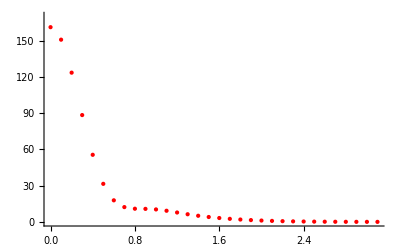

```mathematica
eikp1=ListPlot[%,PlotStyle->Red,PlotRange->{0,170}]
```

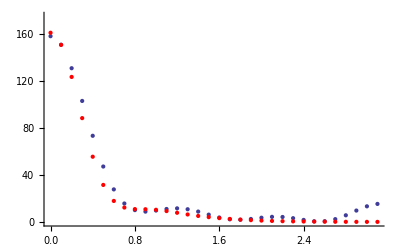

```mathematica
Show[p1,eikp1,PlotRange->{0,175}]
```

```mathematica
Plot[{Abs[f[1,θ]]^2,Abs[Eif[1,θ]]^2},{θ,0,Pi},PlotRange->{0,160}]
```

As you can see above, the two plots actually agree with each other pretty well, at least at small θ. There is some pretty obvious disagreement for large θ, however.

```mathematica
Plot[Abs[Eif[1,θ]]^2,{θ,0,Pi}]
```

## Born Approximation

Here we attempt the Born approximation and compare it to the two methods used above.

```mathematica
Bf[k_,θ_]:=-m/(ℏc^2*k*Sin[θ/2])*NIntegrate[r*V[r]*Sin[2*k*Sin[θ/2]*r],{r,0,Infinity}]
```

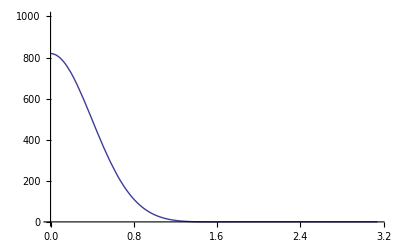

```mathematica
Plot[Abs[Bf[1,θ]]^2,{θ,0,Pi},PlotRange->{{0,Pi},{0,1000}}]
```

Evidently the Born approximation is pretty bad for k=1.

## Check Method for k=10

For k=10, then k^2 = 100 >> 2*m*V/ℏ^2 ~= 2.5, so the eikonal approximation should be valid.

```mathematica
dσdΩ[10]//Timing
```

{414.128,{{0.,796.488},{0.1,24.4686},{0.2,0.254775},{0.3,0.00395207},{0.4,0.00021794},{0.5,1.12015×10^-6},{0.6,5.97535×10^-6},{0.7,2.30653×10^-6},{0.8,1.34707×10^-6},{0.9,6.62009×10^-7},{1.,2.91372×10^-7},{1.1,9.74213×10^-8},{1.2,1.65141×10^-8},{1.3,7.2132×10^-9},{1.4,4.1703×10^-8},{1.5,1.00483×10^-7},{1.6,1.69445×10^-7},{1.7,2.39076×10^-7},{1.8,3.01244×10^-7},{1.9,3.5077×10^-7},{2.,3.84246×10^-7},{2.1,3.99263×10^-7},{2.2,3.95789×10^-7},{2.3,3.73902×10^-7},{2.4,3.35129×10^-7},{2.5,2.82771×10^-7},{2.6,2.18417×10^-7},{2.7,1.49103×10^-7},{2.8,7.99616×10^-8},{2.9,2.30461×10^-8},{3.,8.05833×10^-9},{3.1,2.08537×10^-7}}}

The first number above is the time that command took to evaluate.

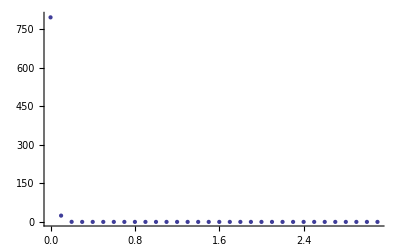

```mathematica
p10=ListPlot[%[[2]],PlotRange->{0,800}]
```

```mathematica
eikdσdΩ[10]//Timing
```

{15.6616,{{0,814.717},{0.1,9.58605},{0.2,0.00263582},{0.3,4.83473×10^-7},{0.4,6.57496×10^-11},{0.5,6.863×10^-15},{0.6,5.57582×10^-19},{0.7,3.24551×10^-23},{0.8,3.20814×10^-24},{0.9,1.45953×10^-23},{1.,4.71617×10^-24},{1.1,1.70782×10^-22},{1.2,6.78913×10^-22},{1.3,2.05549×10^-21},{1.4,1.16117×10^-20},{1.5,1.43788×10^-21},{1.6,2.95138×10^-22},{1.7,7.90299×10^-23},{1.8,1.75778×10^-23},{1.9,1.38346×10^-24},{2.,9.24765×10^-25},{2.1,6.50738×10^-24},{2.2,1.55075×10^-23},{2.3,2.89423×10^-23},{2.4,5.26377×10^-23},{2.5,1.06461×10^-22},{2.6,2.72984×10^-22},{2.7,1.07143×10^-21},{2.8,9.63175×10^-21},{2.9,8.48458×10^-19},{3.,3.87654×10^-18},{3.1,8.50064×10^-19}}}

You can see that as k increases, the eikonal approximation becomes much faster than the partial wave expansion, as we would expect.

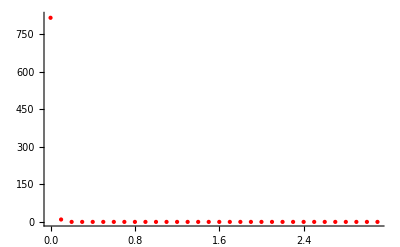

```mathematica
eikp10=ListPlot[%[[2]],PlotStyle->Red,PlotRange->{0,820}]
```

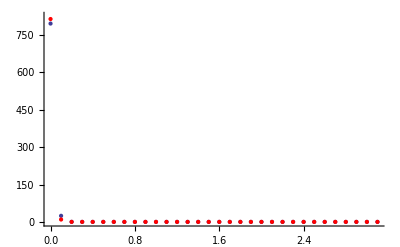

```mathematica
Show[p10,eikp10,PlotRange->{0,825}]
```

## Plots for k=1,2,3

```mathematica
Abs[f[2,0]]^2
```

482.883

```mathematica
Abs[Eif[2,0]]^2
```

508.187

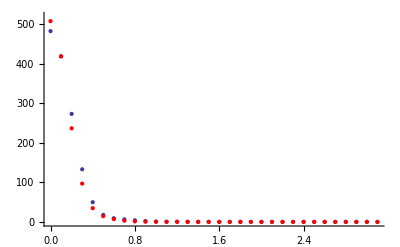

```mathematica
p2=ListPlot[dσdΩ[2]];
eikp2=ListPlot[eikdσdΩ[2],PlotStyle->Red];
Show[p2,eikp2,PlotRange->{0,520}]
```

```mathematica
Abs[f[3,0]]^2
```

636.764

```mathematica
Abs[Eif[3,0]]^2
```

666.489

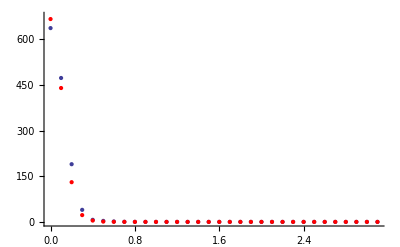

```mathematica
p3=ListPlot[dσdΩ[3]];
eikp3 = ListPlot[eikdσdΩ[3],PlotStyle->Red];
Show[p3,eikp3,PlotRange->{0,675}]
```

## Plot for k=0.1

As you can see below, the approximation gets pretty bad as k -> 0.

```mathematica
Abs[f[.1,0]]^2
```

39.0846

```mathematica
Abs[Eif[.1,0]]^2
```

5.01233

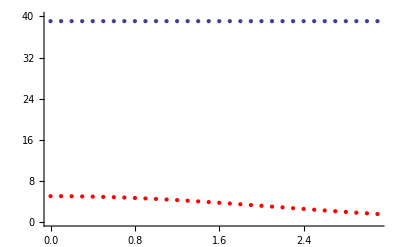

```mathematica
p01=ListPlot[dσdΩ[.1]];
eikp01=ListPlot[eikdσdΩ[.1],PlotStyle->Red];
Show[p01,eikp01,PlotRange->{0,40}]
```